# Illustration figure panel b-d - Preferential Attachment

## Parameters

```mathematica
TextSize=20;
```

```mathematica
TicksSize=15;
```

```mathematica
GraphThickness=0.01;
```

```mathematica
LinesThickness=0.007;
```

```mathematica
ColorsDiscrete=ResourceFunction["HexToColor"]/@{"#e3f4dd","#e2f4dd","#e2f4dc","#e1f3db","#e0f3db","#e0f3da","#dff3d9","#def2d9","#def2d8","#ddf2d7","#dcf2d7","#dcf1d6","#dbf1d5","#daf1d5","#daf0d4","#d9f0d3","#d8f0d3","#d8f0d2","#d7efd1","#d6efd1","#d6efd0","#d5efcf","#d4eecf","#d3eece","#d3eecd","#d2edcd","#d1edcc","#d0edcb","#d0edcb","#cfecca","#ceecca","#cdecc9","#cdebc8","#ccebc8","#cbebc7","#caeac6","#c9eac6","#c8eac5","#c7e9c5","#c6e9c4","#c5e8c4","#c5e8c3","#c4e8c2","#c3e7c2","#c2e7c1","#c1e7c1","#c0e6c0","#bfe6c0","#bde5bf","#bce5bf","#bbe5be","#bae4be","#b9e4be","#b8e3bd","#b7e3bd","#b6e2bd","#b5e2bc","#b3e1bc","#b2e1bc","#b1e1bb","#b0e0bb","#afe0bb","#aedfbb","#acdfbb","#abdeba","#aadeba","#a9ddba","#a7ddba","#a6dcba","#a5dcba","#a3dbba","#a2dbba","#a1daba","#a0daba","#9ed9bb","#9dd9bb","#9cd8bb","#9ad8bb","#99d7bb","#98d7bc","#96d6bc","#95d6bc","#93d5bd","#92d5bd","#91d4bd","#8fd3be","#8ed3be","#8dd2be","#8bd2bf","#8ad1bf","#88d1c0","#87d0c0","#86cfc1","#84cfc1","#83cec1","#81cec2","#80cdc2","#7fccc3","#7dccc3","#7ccbc4","#7acac4","#79cac5","#77c9c5","#76c8c6","#75c8c6","#73c7c7","#72c6c7","#70c5c7","#6fc5c8","#6ec4c8","#6cc3c9","#6bc3c9","#69c2ca","#68c1ca","#67c0ca","#65bfcb","#64bfcb","#63becb","#61bdcc","#60bccc","#5fbbcc","#5dbacc","#5cb9cc","#5ab9cd","#59b8cd","#58b7cd","#57b6cd","#55b5cd","#54b4cd","#53b3cd","#51b2cd","#50b1cd","#4fb0cd","#4eafcd","#4caecd","#4badcc","#4aaccc","#49abcc","#48aacc","#46a9cb","#45a8cb","#44a6cb","#43a5ca","#42a4ca","#41a3c9","#3fa2c9","#3ea1c8","#3da0c8","#3c9ec7","#3b9dc7","#3a9cc6","#399bc6","#379ac5","#3699c5","#3597c4","#3496c4","#3395c3","#3294c2","#3193c2","#3092c1","#2f90c0","#2d8fc0","#2c8ebf","#2b8dbf","#2a8cbe","#298abd","#2889bd","#2788bc","#2687bc","#2586bb","#2485ba","#2383ba","#2282b9","#2081b9","#1f80b8","#1e7fb7","#1d7eb7","#1c7db6","#1b7bb5","#1a7ab5","#1979b4","#1978b3","#1877b3","#1776b2","#1674b1","#1573b0","#1472b0","#1371af","#1370ae","#126fad","#116dac","#106cac","#106bab","#0f6aaa","#0e69a9","#0e67a8","#0d66a7","#0d65a6","#0c64a5","#0c63a4"}
```

{RGBColor[0.8901960784313725, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8862745098039215, 0.9568627450980391, 0.8627450980392157],RGBColor[0.8823529411764706, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8588235294117647],RGBColor[0.8784313725490196, 0.9529411764705882, 0.8549019607843137],RGBColor[0.8745098039215686, 0.9529411764705882, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8509803921568627],RGBColor[0.8705882352941177, 0.9490196078431372, 0.8470588235294118],RGBColor[0.8666666666666667, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9490196078431372, 0.8431372549019608],RGBColor[0.8627450980392157, 0.9450980392156862, 0.8392156862745098],RGBColor[0.8588235294117647, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9450980392156862, 0.8352941176470589],RGBColor[0.8549019607843137, 0.9411764705882353, 0.8313725490196078],RGBColor[0.8509803921568627, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8274509803921568],RGBColor[0.8470588235294118, 0.9411764705882353, 0.8235294117647058],RGBColor[0.8431372549019608, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8196078431372549],RGBColor[0.8392156862745098, 0.9372549019607843, 0.8156862745098039],RGBColor[0.8352941176470589, 0.9372549019607843, 0.8117647058823529],RGBColor[0.8313725490196078, 0.9333333333333333, 0.8117647058823529],RGBColor[0.8274509803921568, 0.9333333333333333, 0.807843137254902],RGBColor[0.8274509803921568, 0.9333333333333333, 0.803921568627451],RGBColor[0.8235294117647058, 0.9294117647058824, 0.803921568627451],RGBColor[0.8196078431372549, 0.9294117647058824, 0.8],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8156862745098039, 0.9294117647058824, 0.796078431372549],RGBColor[0.8117647058823529, 0.9254901960784314, 0.792156862745098],RGBColor[0.807843137254902, 0.9254901960784314, 0.792156862745098],RGBColor[0.803921568627451, 0.9254901960784314, 0.788235294117647],RGBColor[0.803921568627451, 0.9215686274509803, 0.7843137254901961],RGBColor[0.8, 0.9215686274509803, 0.7843137254901961],RGBColor[0.796078431372549, 0.9215686274509803, 0.7803921568627451],RGBColor[0.792156862745098, 0.9176470588235294, 0.7764705882352941],RGBColor[0.788235294117647, 0.9176470588235294, 0.7764705882352941],RGBColor[0.7843137254901961, 0.9176470588235294, 0.7725490196078432],RGBColor[0.7803921568627451, 0.9137254901960784, 0.7725490196078432],RGBColor[0.7764705882352941, 0.9137254901960784, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7686274509803921],RGBColor[0.7725490196078432, 0.9098039215686274, 0.7647058823529411],RGBColor[0.7686274509803921, 0.9098039215686274, 0.7607843137254902],RGBColor[0.7647058823529411, 0.9058823529411765, 0.7607843137254902],RGBColor[0.7607843137254902, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7568627450980392, 0.9058823529411765, 0.7568627450980392],RGBColor[0.7529411764705882, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7490196078431373, 0.9019607843137255, 0.7529411764705882],RGBColor[0.7411764705882353, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7372549019607844, 0.8980392156862745, 0.7490196078431373],RGBColor[0.7333333333333333, 0.8980392156862745, 0.7450980392156863],RGBColor[0.7294117647058823, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7254901960784313, 0.8941176470588235, 0.7450980392156863],RGBColor[0.7215686274509804, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7176470588235294, 0.8901960784313725, 0.7411764705882353],RGBColor[0.7137254901960784, 0.8862745098039215, 0.7411764705882353],RGBColor[0.7098039215686275, 0.8862745098039215, 0.7372549019607844],RGBColor[0.7019607843137254, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6980392156862745, 0.8823529411764706, 0.7372549019607844],RGBColor[0.6941176470588235, 0.8823529411764706, 0.7333333333333333],RGBColor[0.6901960784313725, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6862745098039216, 0.8784313725490196, 0.7333333333333333],RGBColor[0.6823529411764706, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6745098039215687, 0.8745098039215686, 0.7333333333333333],RGBColor[0.6705882352941176, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6666666666666666, 0.8705882352941177, 0.7294117647058823],RGBColor[0.6627450980392157, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6549019607843137, 0.8666666666666667, 0.7294117647058823],RGBColor[0.6509803921568628, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6470588235294118, 0.8627450980392157, 0.7294117647058823],RGBColor[0.6392156862745098, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6352941176470588, 0.8588235294117647, 0.7294117647058823],RGBColor[0.6313725490196078, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6274509803921569, 0.8549019607843137, 0.7294117647058823],RGBColor[0.6196078431372549, 0.8509803921568627, 0.7333333333333333],RGBColor[0.615686274509804, 0.8509803921568627, 0.7333333333333333],RGBColor[0.611764705882353, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6039215686274509, 0.8470588235294118, 0.7333333333333333],RGBColor[0.6, 0.8431372549019608, 0.7333333333333333],RGBColor[0.596078431372549, 0.8431372549019608, 0.7372549019607844],RGBColor[0.5882352941176471, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5843137254901961, 0.8392156862745098, 0.7372549019607844],RGBColor[0.5764705882352941, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5725490196078431, 0.8352941176470589, 0.7411764705882353],RGBColor[0.5686274509803921, 0.8313725490196078, 0.7411764705882353],RGBColor[0.5607843137254902, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5568627450980392, 0.8274509803921568, 0.7450980392156863],RGBColor[0.5529411764705883, 0.8235294117647058, 0.7450980392156863],RGBColor[0.5450980392156862, 0.8235294117647058, 0.7490196078431373],RGBColor[0.5411764705882353, 0.8196078431372549, 0.7490196078431373],RGBColor[0.5333333333333333, 0.8196078431372549, 0.7529411764705882],RGBColor[0.5294117647058824, 0.8156862745098039, 0.7529411764705882],RGBColor[0.5254901960784314, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5176470588235293, 0.8117647058823529, 0.7568627450980392],RGBColor[0.5137254901960784, 0.807843137254902, 0.7568627450980392],RGBColor[0.5058823529411764, 0.807843137254902, 0.7607843137254902],RGBColor[0.5019607843137255, 0.803921568627451, 0.7607843137254902],RGBColor[0.4980392156862745, 0.8, 0.7647058823529411],RGBColor[0.49019607843137253, 0.8, 0.7647058823529411],RGBColor[0.48627450980392156, 0.796078431372549, 0.7686274509803921],RGBColor[0.4784313725490196, 0.792156862745098, 0.7686274509803921],RGBColor[0.4745098039215686, 0.792156862745098, 0.7725490196078432],RGBColor[0.4666666666666667, 0.788235294117647, 0.7725490196078432],RGBColor[0.4627450980392157, 0.7843137254901961, 0.7764705882352941],RGBColor[0.4588235294117647, 0.7843137254901961, 0.7764705882352941],RGBColor[0.45098039215686275, 0.7803921568627451, 0.7803921568627451],RGBColor[0.44705882352941173, 0.7764705882352941, 0.7803921568627451],RGBColor[0.4392156862745098, 0.7725490196078432, 0.7803921568627451],RGBColor[0.43529411764705883, 0.7725490196078432, 0.7843137254901961],RGBColor[0.43137254901960786, 0.7686274509803921, 0.7843137254901961],RGBColor[0.4235294117647059, 0.7647058823529411, 0.788235294117647],RGBColor[0.4196078431372549, 0.7647058823529411, 0.788235294117647],RGBColor[0.4117647058823529, 0.7607843137254902, 0.792156862745098],RGBColor[0.40784313725490196, 0.7568627450980392, 0.792156862745098],RGBColor[0.403921568627451, 0.7529411764705882, 0.792156862745098],RGBColor[0.396078431372549, 0.7490196078431373, 0.796078431372549],RGBColor[0.39215686274509803, 0.7490196078431373, 0.796078431372549],RGBColor[0.38823529411764707, 0.7450980392156863, 0.796078431372549],RGBColor[0.3803921568627451, 0.7411764705882353, 0.8],RGBColor[0.3764705882352941, 0.7372549019607844, 0.8],RGBColor[0.37254901960784315, 0.7333333333333333, 0.8],RGBColor[0.36470588235294116, 0.7294117647058823, 0.8],RGBColor[0.3607843137254902, 0.7254901960784313, 0.8],RGBColor[0.3529411764705882, 0.7254901960784313, 0.803921568627451],RGBColor[0.34901960784313724, 0.7215686274509804, 0.803921568627451],RGBColor[0.34509803921568627, 0.7176470588235294, 0.803921568627451],RGBColor[0.3411764705882353, 0.7137254901960784, 0.803921568627451],RGBColor[0.3333333333333333, 0.7098039215686275, 0.803921568627451],RGBColor[0.32941176470588235, 0.7058823529411764, 0.803921568627451],RGBColor[0.3254901960784314, 0.7019607843137254, 0.803921568627451],RGBColor[0.3176470588235294, 0.6980392156862745, 0.803921568627451],RGBColor[0.3137254901960784, 0.6941176470588235, 0.803921568627451],RGBColor[0.30980392156862746, 0.6901960784313725, 0.803921568627451],RGBColor[0.3058823529411765, 0.6862745098039216, 0.803921568627451],RGBColor[0.2980392156862745, 0.6823529411764706, 0.803921568627451],RGBColor[0.29411764705882354, 0.6784313725490196, 0.8],RGBColor[0.2901960784313725, 0.6745098039215687, 0.8],RGBColor[0.28627450980392155, 0.6705882352941176, 0.8],RGBColor[0.2823529411764706, 0.6666666666666666, 0.8],RGBColor[0.27450980392156865, 0.6627450980392157, 0.796078431372549],RGBColor[0.27058823529411763, 0.6588235294117647, 0.796078431372549],RGBColor[0.26666666666666666, 0.6509803921568628, 0.796078431372549],RGBColor[0.2627450980392157, 0.6470588235294118, 0.792156862745098],RGBColor[0.2588235294117647, 0.6431372549019607, 0.792156862745098],RGBColor[0.2549019607843137, 0.6392156862745098, 0.788235294117647],RGBColor[0.24705882352941178, 0.6352941176470588, 0.788235294117647],RGBColor[0.24313725490196078, 0.6313725490196078, 0.7843137254901961],RGBColor[0.2392156862745098, 0.6274509803921569, 0.7843137254901961],RGBColor[0.23529411764705882, 0.6196078431372549, 0.7803921568627451],RGBColor[0.23137254901960785, 0.615686274509804, 0.7803921568627451],RGBColor[0.22745098039215686, 0.611764705882353, 0.7764705882352941],RGBColor[0.22352941176470587, 0.6078431372549019, 0.7764705882352941],RGBColor[0.21568627450980393, 0.6039215686274509, 0.7725490196078432],RGBColor[0.21176470588235294, 0.6, 0.7725490196078432],RGBColor[0.20784313725490194, 0.592156862745098, 0.7686274509803921],RGBColor[0.20392156862745098, 0.5882352941176471, 0.7686274509803921],RGBColor[0.2, 0.5843137254901961, 0.7647058823529411],RGBColor[0.19607843137254902, 0.580392156862745, 0.7607843137254902],RGBColor[0.19215686274509802, 0.5764705882352941, 0.7607843137254902],RGBColor[0.18823529411764706, 0.5725490196078431, 0.7568627450980392],RGBColor[0.1843137254901961, 0.5647058823529412, 0.7529411764705882],RGBColor[0.1764705882352941, 0.5607843137254902, 0.7529411764705882],RGBColor[0.17254901960784313, 0.5568627450980392, 0.7490196078431373],RGBColor[0.16862745098039217, 0.5529411764705883, 0.7490196078431373],RGBColor[0.16470588235294117, 0.5490196078431373, 0.7450980392156863],RGBColor[0.16078431372549018, 0.5411764705882353, 0.7411764705882353],RGBColor[0.1568627450980392, 0.5372549019607843, 0.7411764705882353],RGBColor[0.15294117647058825, 0.5333333333333333, 0.7372549019607844],RGBColor[0.14901960784313725, 0.5294117647058824, 0.7372549019607844],RGBColor[0.14509803921568626, 0.5254901960784314, 0.7333333333333333],RGBColor[0.1411764705882353, 0.5215686274509804, 0.7294117647058823],RGBColor[0.13725490196078433, 0.5137254901960784, 0.7294117647058823],RGBColor[0.13333333333333333, 0.5098039215686274, 0.7254901960784313],RGBColor[0.12549019607843137, 0.5058823529411764, 0.7254901960784313],RGBColor[0.12156862745098039, 0.5019607843137255, 0.7215686274509804],RGBColor[0.11764705882352941, 0.4980392156862745, 0.7176470588235294],RGBColor[0.11372549019607843, 0.49411764705882355, 0.7176470588235294],RGBColor[0.10980392156862745, 0.49019607843137253, 0.7137254901960784],RGBColor[0.10588235294117647, 0.4823529411764706, 0.7098039215686275],RGBColor[0.10196078431372549, 0.4784313725490196, 0.7098039215686275],RGBColor[0.09803921568627451, 0.4745098039215686, 0.7058823529411764],RGBColor[0.09803921568627451, 0.47058823529411764, 0.7019607843137254],RGBColor[0.09411764705882353, 0.4666666666666667, 0.7019607843137254],RGBColor[0.09019607843137255, 0.4627450980392157, 0.6980392156862745],RGBColor[0.08627450980392157, 0.4549019607843137, 0.6941176470588235],RGBColor[0.08235294117647059, 0.45098039215686275, 0.6901960784313725],RGBColor[0.0784313725490196, 0.44705882352941173, 0.6901960784313725],RGBColor[0.07450980392156863, 0.44313725490196076, 0.6862745098039216],RGBColor[0.07450980392156863, 0.4392156862745098, 0.6823529411764706],RGBColor[0.07058823529411765, 0.43529411764705883, 0.6784313725490196],RGBColor[0.06666666666666667, 0.42745098039215684, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4235294117647059, 0.6745098039215687],RGBColor[0.06274509803921569, 0.4196078431372549, 0.6705882352941176],RGBColor[0.058823529411764705, 0.4156862745098039, 0.6666666666666666],RGBColor[0.054901960784313725, 0.4117647058823529, 0.6627450980392157],RGBColor[0.054901960784313725, 0.403921568627451, 0.6588235294117647],RGBColor[0.050980392156862744, 0.4, 0.6549019607843137],RGBColor[0.050980392156862744, 0.396078431372549, 0.6509803921568628],RGBColor[0.047058823529411764, 0.39215686274509803, 0.6470588235294118],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
ColorGradient=Blend[ColorsDiscrete,#]&
```

Blend[ColorsDiscrete,#1]&

## Panel b

## Load the Data

```mathematica
CrimeList={"Violent_Crime"}
```

{Violent_Crime}

```mathematica
YearsList=Range[2006,2023]
```

{2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

```mathematica
City="NYC"
```

NYC

### Specific block

```mathematica
SetDirectory["..."]
```

#### xxx

```mathematica
AnnualCrimesBlock=Flatten[Import["crimes_violent_xxx.mat"]]
```

{5.,4.,7.,4.,6.,9.,11.,11.,5.,10.,18.,24.,20.,20.,23.,21.,26.,25.}

```mathematica
TotalCrimesBlock=Flatten[Import["total_crimes_violent_xxx.mat"]]
```

{5.,9.,16.,20.,26.,35.,46.,57.,62.,72.,90.,114.,134.,154.,177.,198.,224.,249.}

```mathematica
BlockData=Partition[Riffle[TotalCrimesBlock[[1;;-2]],AnnualCrimesBlock[[2;;-1]]],2]
```

{{5.,4.},{9.,7.},{16.,4.},{20.,6.},{26.,9.},{35.,11.},{46.,11.},{57.,5.},{62.,10.},{72.,18.},{90.,24.},{114.,20.},{134.,20.},{154.,23.},{177.,21.},{198.,26.},{224.,25.}}

### All the rest

```mathematica
SetDirectory["..."]
```

```mathematica
DataNYCNames={};
```

```mathematica
Do[cleanCrime=StringReplace[crime,"_"->""];fileName=StringJoin["PA_Data_mblock_",crime,"_Year_",ToString[year],"_",City,".mat"];
data=Flatten[Import[fileName],1];
varName="Data"<>City<>cleanCrime<>ToString[year];
ToExpression[varName<>" = data"];
AppendTo[DataNYCNames,varName];,{crime,CrimeList},{year,YearsList[[2;;-1]]}]
```

```mathematica
DataNYCNames
```

{DataNYCViolentCrime2007,DataNYCViolentCrime2008,DataNYCViolentCrime2009,DataNYCViolentCrime2010,DataNYCViolentCrime2011,DataNYCViolentCrime2012,DataNYCViolentCrime2013,DataNYCViolentCrime2014,DataNYCViolentCrime2015,DataNYCViolentCrime2016,DataNYCViolentCrime2017,DataNYCViolentCrime2018,DataNYCViolentCrime2019,DataNYCViolentCrime2020,DataNYCViolentCrime2021,DataNYCViolentCrime2022,DataNYCViolentCrime2023}

```mathematica
mBlockData=Table[Select[ToExpression[DataNYCNames[[i]]],#[[1]]=!=0.0&],{i,1,Length[DataNYCNames]}]
```

### All the data

```mathematica
SetDirectory["..."]
```

```mathematica
FullDataNYCNames={};
```

```mathematica
Do[cleanCrime=StringReplace[crime,"_"->""];fileName=StringJoin["All_PA_Data_",crime,"_Year_",ToString[year],"_",City,".mat"];
data=Flatten[Import[fileName],1];
varName="AllData"<>City<>cleanCrime<>ToString[year];
ToExpression[varName<>" = data"];
AppendTo[FullDataNYCNames,varName];,{crime,CrimeList},{year,YearsList[[2;;-1]]}]
```

```mathematica
FullDataNYCNames
```

{AllDataNYCViolentCrime2007,AllDataNYCViolentCrime2008,AllDataNYCViolentCrime2009,AllDataNYCViolentCrime2010,AllDataNYCViolentCrime2011,AllDataNYCViolentCrime2012,AllDataNYCViolentCrime2013,AllDataNYCViolentCrime2014,AllDataNYCViolentCrime2015,AllDataNYCViolentCrime2016,AllDataNYCViolentCrime2017,AllDataNYCViolentCrime2018,AllDataNYCViolentCrime2019,AllDataNYCViolentCrime2020,AllDataNYCViolentCrime2021,AllDataNYCViolentCrime2022,AllDataNYCViolentCrime2023}

```mathematica
AllBlocksData=Table[Select[ToExpression[FullDataNYCNames[[i]]],#[[1]]=!=0.0&],{i,1,Length[FullDataNYCNames]}]
```

## Plotting

## Panel b

```mathematica
colors=ColorGradient/@Rescale[Range[Length[YearsList]]]
```

{RGBColor[0.8901960784313725, 0.9568627450980391, 0.8666666666666667],RGBColor[0.8599769319492503, 0.9450980392156862, 0.8364475201845444],RGBColor[0.8274509803921568, 0.9333333333333333, 0.8062283737024222],RGBColor[0.7916955017301037, 0.9176470588235294, 0.7764705882352941],RGBColor[0.7497116493656286, 0.9019607843137255, 0.7529411764705882],RGBColor[0.6959630911188004, 0.8823529411764706, 0.7351787773933103],RGBColor[0.6382929642445213, 0.8588235294117647, 0.7294117647058823],RGBColor[0.5769319492502883, 0.8355247981545559, 0.7409457900807382],RGBColor[0.5151095732410611, 0.8092272202998847, 0.7568627450980392],RGBColor[0.44959630911188003, 0.7790080738177624, 0.7803921568627451],RGBColor[0.38777393310265285, 0.7448673587081892, 0.796309111880046],RGBColor[0.3264129181084198, 0.7028835063437139, 0.803921568627451],RGBColor[0.2687427912341407, 0.6551326412918108, 0.796078431372549],RGBColor[0.21499423298731257, 0.6032295271049596, 0.7725490196078432],RGBColor[0.1651672433679354, 0.5494809688581316, 0.7455594002306806],RGBColor[0.11534025374855825, 0.49573241061130335, 0.7176470588235294],RGBColor[0.07450980392156863, 0.4419838523644752, 0.685121107266436],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
colors=colors[[2;;-1]]
```

{RGBColor[0.8599769319492503, 0.9450980392156862, 0.8364475201845444],RGBColor[0.8274509803921568, 0.9333333333333333, 0.8062283737024222],RGBColor[0.7916955017301037, 0.9176470588235294, 0.7764705882352941],RGBColor[0.7497116493656286, 0.9019607843137255, 0.7529411764705882],RGBColor[0.6959630911188004, 0.8823529411764706, 0.7351787773933103],RGBColor[0.6382929642445213, 0.8588235294117647, 0.7294117647058823],RGBColor[0.5769319492502883, 0.8355247981545559, 0.7409457900807382],RGBColor[0.5151095732410611, 0.8092272202998847, 0.7568627450980392],RGBColor[0.44959630911188003, 0.7790080738177624, 0.7803921568627451],RGBColor[0.38777393310265285, 0.7448673587081892, 0.796309111880046],RGBColor[0.3264129181084198, 0.7028835063437139, 0.803921568627451],RGBColor[0.2687427912341407, 0.6551326412918108, 0.796078431372549],RGBColor[0.21499423298731257, 0.6032295271049596, 0.7725490196078432],RGBColor[0.1651672433679354, 0.5494809688581316, 0.7455594002306806],RGBColor[0.11534025374855825, 0.49573241061130335, 0.7176470588235294],RGBColor[0.07450980392156863, 0.4419838523644752, 0.685121107266436],RGBColor[0.047058823529411764, 0.38823529411764707, 0.6431372549019607]}

```mathematica
n=Length[colors]
```

17

```mathematica
years=YearsList[[2;;-1]]
```

{2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023}

```mathematica
colorBar=Graphics[Table[{colors[[i]],EdgeForm[White],Rectangle[{0,i-1},{2,i}]},{i,1,n}],Frame->True,FrameStyle->White,FrameTicks->{{None,None},{{{1,ToString[years[[1]]]}},{{1,ToString[years[[-1]]]}}}},FrameTicksStyle->Directive[FontFamily->"Arial",FontSize->TicksSize,Black],ImageSize->35]
```

-Graphics-

```mathematica
MainPanelB=ListLogLogPlot[Reverse[mBlockData],PlotRange->{{0.5,10^4},{0.5,10^3}},PlotMarkers->Table[Graphics[{Directive[colors[[n-i+1]],Opacity[0.35]],Circle[]},ImageSize->10]
,{i,1,Length[years]}],Frame->True,AspectRatio->1,Background->White,FrameTicksStyle->1.1017*TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],GridLines->{{10^0,10^1,10^2,10^3,10^4},{10^0,10^1,10^2,10^3,10^4}},FrameLabel->{Style["S_(b, t - 1)",Italic,TextSize,FontFamily->"Arial"],Style["C_(b, t)",Italic,TextSize,FontFamily->"Arial"]},FrameTicks->{{{{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}}, None},{{{10^0,"10^0"},{10^1,"10^1"},{10^2,"10^2"},{10^3,"10^3"},{10^4,"10^4"}}, None}},ImageSize->{360,320}];
```

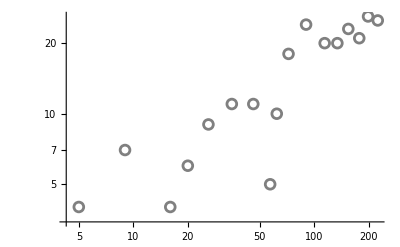

```mathematica
BlockPlot=ListLogLogPlot[{BlockData},PlotMarkers->Graphics[{Gray,Circle[]},ImageSize->10]]
```

```mathematica
Export["NYC Illustration Figure Panel b.pdf",Show[MainPanelB,BlockPlot]]
```

NYC Illustration Figure Panel b.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["NYC Illustration Figure Panel b.pdf"]]]
```

## Panel c

### Calculate the averages

```mathematica
AllBlocksAverages=Map[Function[dataset,{#1,Mean[#2[[All,2]]]}&@@@Normal@GroupBy[dataset,First]],AllBlocksData]
```

```mathematica
AllBlocksAveragesNorm=AllBlocksAverages/. l:{{_,_}..}:>Module[{total=Total[l[[All,2]]]},l/. {x_,y_}:>{x,y/total}]
```

### Plotting

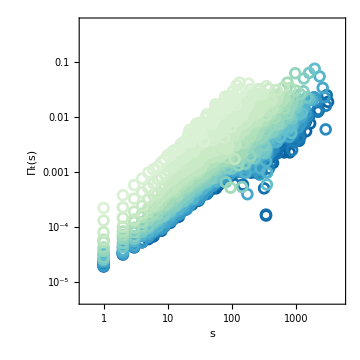

```mathematica
MainPanelC=ListLogLogPlot[Reverse[AllBlocksAveragesNorm],PlotRange->{{5*0.1,5*10^3},{5*10^-6,5*10^-1}},PlotMarkers->Table[Graphics[{Directive[colors[[n-i+1]],Opacity[1]],Circle[]},ImageSize->10]
,{i,1,Length[years]}],Frame->True,AspectRatio->1,Background->White,FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],GridLines->{{5*10^-1,5*10^0,5*10^1,5*10^2,5*10^3},{5*10^-6,5*10^-5,5*10^-4,5*10^-3,5*10^-2}},FrameLabel->{Style[TraditionalForm[s],TextSize,FontFamily->"Arial"],Style[TraditionalForm[Subscript[Π,t][s]],TextSize,FontFamily->"Arial"]},FrameTicks->{{{{5*10^-6,"5×10^-6"},{5*10^-5,"5×10^-5"},{5×10^-4,"5×10^-4"},{5×10^-3,"5×10^-3"},{5×10^-2,"5×10^-2"},{5×10^-1,"5×10^-1"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},ImageSize->{360,320}]
```

## Panel d

### Calculate the averages

```mathematica
AllBlocksCumulative=Map[Function[dataset,Module[{sorted,ys,cumYs},sorted=SortBy[dataset,First];ys=sorted[[All,2]];
cumYs=Accumulate[ys];
Transpose[{sorted[[All,1]],cumYs}]]],AllBlocksAveragesNorm]
```

### Plotting

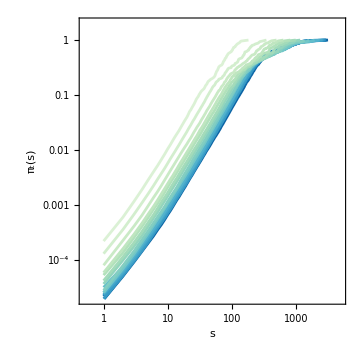

```mathematica
MainPanelD=ListLogLogPlot[Reverse[AllBlocksCumulative],PlotRange->{{5*0.1,5*10^3},{2*10^-5,2}},Joined->True,PlotStyle->Table[Directive[colors[[n-i+1]],Opacity[1]],{i,1,Length[years]}],Frame->True,AspectRatio->1,Background->White,FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.006]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],GridLines->{{5*10^-1,5*10^0,5*10^1,5*10^2,5*10^3},{2*10^-5,2*10^-4,2*10^-3,2*10^-2,2*10^-1}},FrameLabel->{Style[TraditionalForm[s],TextSize,FontFamily->"Arial"],Style[TraditionalForm[Subscript[π,t][s]],TextSize,FontFamily->"Arial"]},FrameTicks->{{{{2*10^-6,"2×10^-6"},{2*10^-5,"2×10^-5"},{2*10^-4,"2×10^-4"},{2*10^-3,"2×10^-3"},{2*10^-2,"2×10^-2"},{2*10^-1,"2×10^-1"},{2*10^0,"2×10^0"}},None},{{{5×10^-1,"5×10^-1"},{5×10^0,"5×10^0"},{5×10^1,"5×10^1"},{5×10^2,"5×10^2"},{5×10^3,"5×10^3"}},None}},ImageSize->{360,320}]
```